# Figure 1

```mathematica
H[q_,p_,gg_]=(q^2+p^2)/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
V[q_,gg_]=q^2/2-(1/2)*(1+(Sqrt[2]*gg*q)^2)^(1/2);
```

#### g=1/2^(1/2)

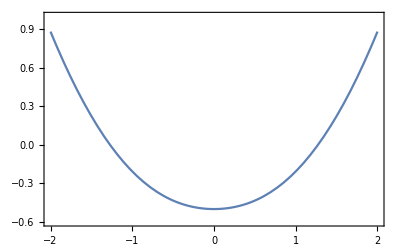

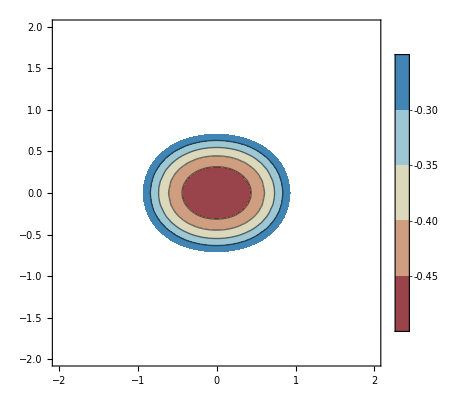

```mathematica
g=1/2^(1/2);
figpot=pot=Show[Plot[V[q,g],{q,-2,2},PlotRange->{{-2,2},{-0.6,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=contour=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.6,-0.25}},LabelStyle->{22,Black},PlotLegends->Automatic,ColorFunction->"RedBlueTones"]
```

#### g=0.95

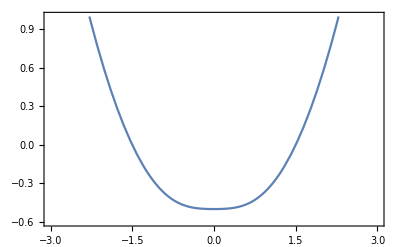

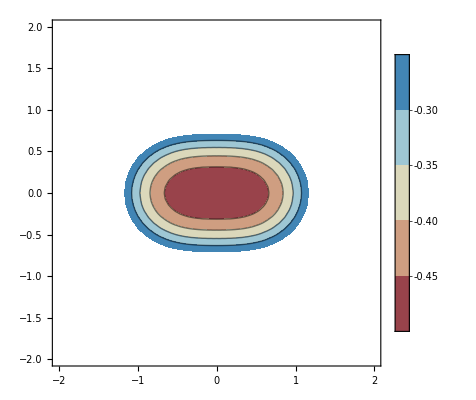

```mathematica
g=0.95;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-0.6,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.65,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=1.05

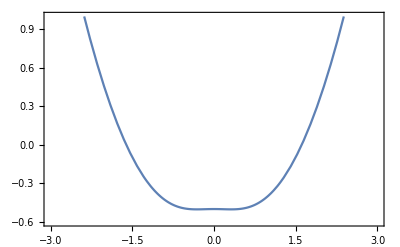

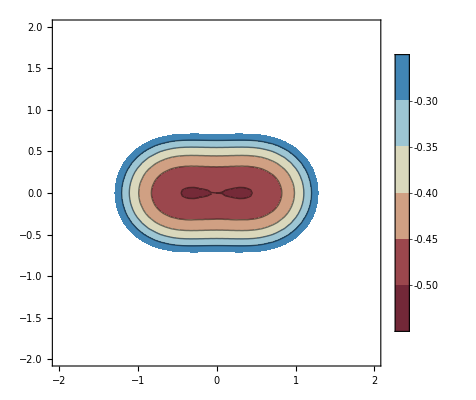

```mathematica
g=1.05;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-0.6,1.0}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.65,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=2^(1/2)

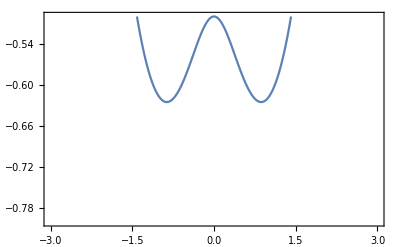

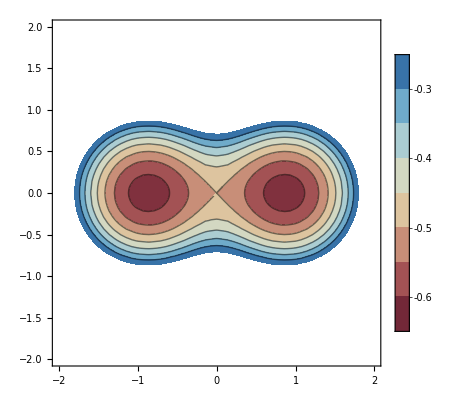

```mathematica
g=2^(1/2);
figpot=Show[Plot[V[q,g],{q,-3,3},Frame->True,Axes->False,PlotRange->{{-3,3},{-0.8,-0.5}},LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-0.75,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},ColorFunction->"RedBlueTones"]
```

#### g=2

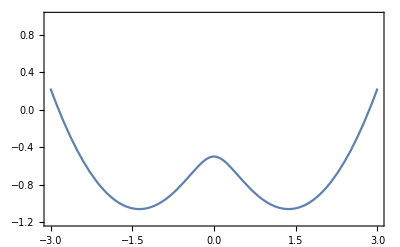

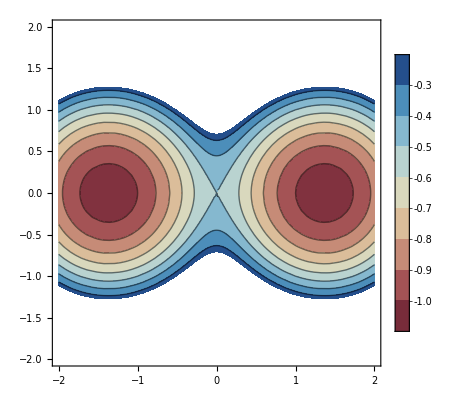

```mathematica
g=2;
figpot=Show[Plot[V[q,g],{q,-3,3},PlotRange->{{-3,3},{-1.2,1}},Frame->True,Axes->False,LabelStyle->{Black,15}],Plot[{},{x,-1.75,1.75},PlotStyle->{{Dashed,Gray}}]]

figcont=ContourPlot[H[q,p,g],{q,-2,2},{p,-2,2},PlotRange->{Automatic,Automatic,{-1.25,-0.25}},PlotLegends->Automatic,LabelStyle->{22,Black},PerformanceGoal->"Accuracy",ColorFunction->"RedBlueTones"]
```

```mathematica
Export["Veff5.png",figpot]
```

Veff5.png

```mathematica
Export["phasespace1.png",figcont]
```

phasespace1.png